# Normalized Additional Velocity (NAV)

By Davi Rodrigues & Alejandro Hernandez-Arboleda
March, 2022

The method is described in detail in the paper:
  Normalized Additional Velocity: a fast sample analysis for dark matter or modified gravity models
  A.Hernandez-Arboleda, D.C. Rodrigues, A.Wojnar

## 0. Prelude

```mathematica
isBurkertWithGaussianPriors = True; (*Loads the Burkert data with Gaussian priors (True), or the fixed case (False)*)

SetDirectory[NotebookDirectory[]];
<<NAVbaseCode.wl;
<<NAVoptions.wl;

SetDirectory[FileNameJoin[{NotebookDirectory[], "Output"}]];

If[isBurkertWithGaussianPriors,
  exportBurkertIndividualResultsGaussian,
  (*else*)
  exportBurkertIndividualResultsFixed
];
```

## I. Observational NAV

## I.1. Kernel Density Estimation for the distribution

All RAR galaxies case:

Gaussian bandwidths from Silverman rule of thumb:   {0.0676207,0.0820401}

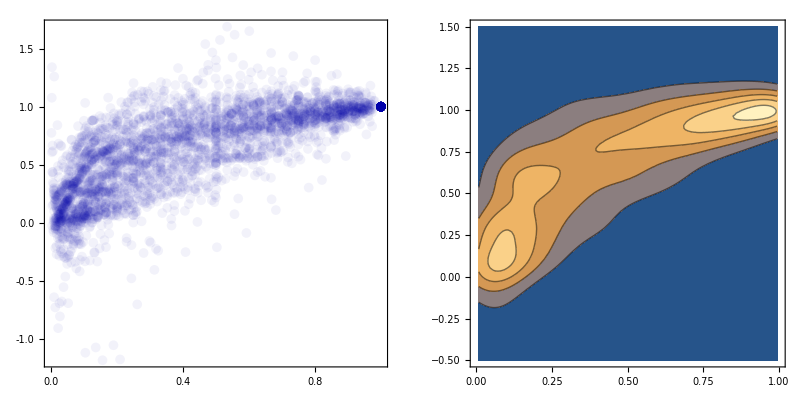

Only the bulgeless RAR galaxies:

Gaussian bandwidths from Silverman rule of thumb:   {0.0724175,0.0867233}

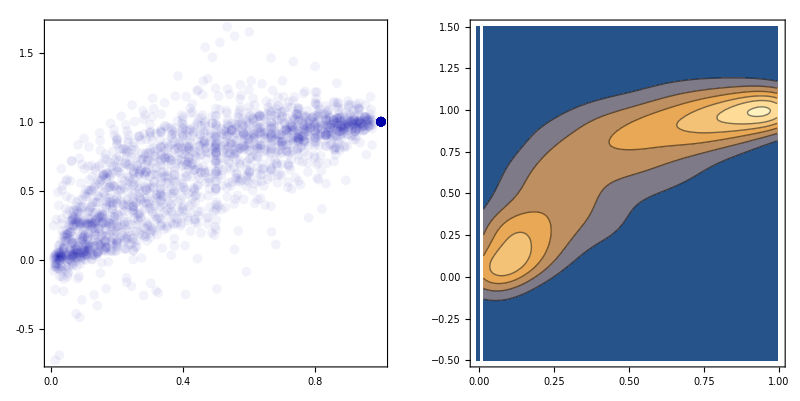

```mathematica
Clear[distributionSilverman, plotBlueZero, statusKDE];

distributionSilverman[dataForKDE_] := distributionSilverman[dataForKDE] = SmoothKernelDistribution[
  dataForKDE, 
  silvermanBw[dataForKDE], 
  "Gaussian", 
  MaxExtraBandwidths -> {{0,0}, {2,2}}, 
  (* No extension for the horizontal axis: there cannot be data lower than 0 and higher than 1,
   extension of 2 bandwidths in the vertical axis: relevant for a few models.*)
  InterpolationPoints -> 200
]; (*Apart from MaxExtraBandwidths and InterpolationPoints, these are the standard options for SmoothKernelDistribution*)
  

plotBlueZero[dataForKDE_, opts:OptionsPattern[]] := nListPlot[
  {dataForKDE}, 
  PlotMarkers -> {
    Graphics[{Darker[Blue],Opacity[0.05],Disk[]}, ImageSize -> 10], 
    Graphics[{Darker[Red],Opacity[0.3],Disk[]}, ImageSize -> 10]
  },
  opts,
  PlotRange -> {{0,1}, All},
  AspectRatio -> 1
];

statusKDE[dataForKDE_, {{xmin_, xmax_}, {ymin_, ymax_}}]:= Block[{},
  Echo[silvermanBw[dataForKDE], 
    "Gaussian bandwidths from Silverman rule of thumb: "
  ];
  Print@GraphicsRow[
    {
      plotBlueZero[dataForKDE], 
      ContourPlot[PDF[distributionSilverman[dataForKDE], {x, y}], {x, xmin, xmax}, {y, ymin, ymax}]
    }
  ]
];


(* SPECIFIC DEFINITIONS *)

Clear[gdRList, gdRListFlat];

gdRList[gdFunction_] := gdRList[gdFunction] = gdFunction[{nRad, δVms}][[#]] & /@ Range[175];
gdRListFlat[gdFunction_] := Flatten[gdRList[gdFunction], 1];

list2RARRot = gdRListFlat @ gdR;
list2RARRotNoBulge = gdRListFlat @ gdRBulgeless; 


(*EXECUTION*)

distRARRot = distributionSilverman[list2RARRot];
distRARRotNoBulge = distributionSilverman[list2RARRotNoBulge];

Echo["All RAR galaxies case:"];
statusKDE[list2RARRot, {{0, 1}, {-0.5, 1.5}}];
Echo["Only the bulgeless RAR galaxies:"];
statusKDE[list2RARRotNoBulge, {{-0.01,1}, {-0.5, 1.5}}];
```

## I.2. The 1σ and 2σ Highest Density Regions

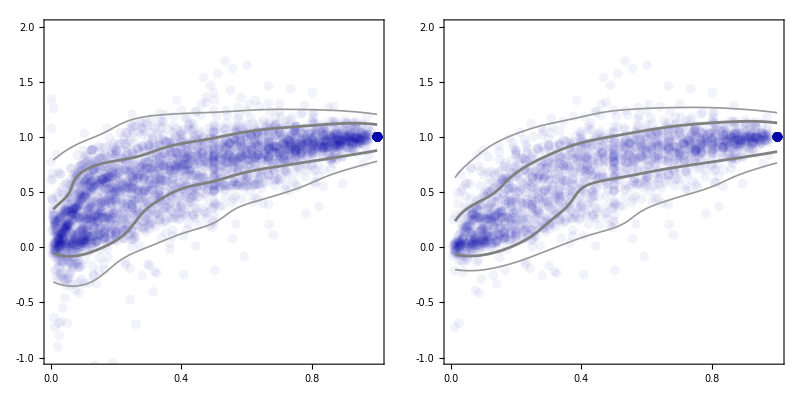

```mathematica
Clear[plotBlue, plotSigmaContours, plotBlueFunction];
(*list1LimitingPDFValues::usage = 
  "limitingPDFValues[data, {{xmin, xmax, xstep}, {ymin, ymax, ystep}}] provides {pdf1Sigma, pdf2sigma}}, \n " <>
  "where pdf1Sigma and pdf2Sigma are respectively the pdf values that limit the 1 or 2 Sigma highest denstiy region found from the KDE of the provided data. \n"<>
  "xmin, xmax, ymin and ymax set the region to be considered, while xstep and ystep the step size to be used to explore the distribution.";
*)  

oneSigmaProbability = NProbability[Less[-1, x, 1], Distributed[x, NormalDistribution[]]];
twoSigmaProbability = NProbability[Less[-2, x, 2], Distributed[x, NormalDistribution[]]];  
  
FindHDPDFValues::usage = "FindHDPDFValues[dist, probabilityList] yeilds a list of the PDF values that dermines the highest density probability regions, these PDF values correspond to the provided list of probabilities (probabilityList). FindHDPDFValues works for DataDistribution of any dimensions. It uses the discrete PDF table provided by dist[\"PDFValues\"], if higher resolution is desirable, increase the numbers of InterpolationPoints when generating the distribution (for instance, in SmoothKernelDistribution).";
FindHDPDFValues[dist_DataDistribution, probability_List] := Block[
  {pdfList, pdfSortList, cdfSortList, positionAtCdf, positionsAtPdf},
  pdfList = dist["PDFValues"];
  pdfSortList = Reverse @ Sort @ pdfList;
  cdfSortList = Accumulate[pdfSortList] / Total[pdfSortList];
  positionAtCdf[prob_] := FirstPosition[cdfSortList, p_ /; p >= prob];
  positionsAtPdf = Flatten[positionAtCdf /@  probability];
  pdfSortList⟦positionsAtPdf⟧
];

plotSigmaContours[dataForContours_, limitingPdfValues_, {{xmin_, xmax_}, {ymin_, ymax_}}, options___]:= Block[
  {pdf}, 
  pdf[x_,y_] = PDF[distributionSilverman[dataForContours], {x, y}]; 
  ContourPlot[
    pdf[x, y],
    {x, xmin, xmax},
    {y, ymin, ymax},
    Contours -> limitingPdfValues, (*Can be the output from FindHDPDFValues*)
    ContourShading -> None, 
    ContourStyle -> {
      {Thickness[0.003], Lighter[Gray, 0.2]},
      {Thickness @ 0.005, Gray}
    },
    options
  ]
];

plotBlue[dataForBluePlot_, limitingPdfValeus_, {{xmin_, xmax_}, {ymin_, ymax_}}, options___] := Show[
  plotBlueZero[dataForBluePlot, options],
  plotSigmaContours[dataForBluePlot, limitingPdfValeus, {{xmin, xmax}, {ymin, ymax}}, PlotRange -> All]
];

(* SPECIFIC DEFINITIONS *)

ymin = -1.5;
ymax = 2.5;
xmin= 0;
xmax = 1;
xstep = 0.005;
ystep = 0.005;

oneAndTwoSigma = {oneSigmaProbability, twoSigmaProbability};
list1Limits = FindHDPDFValues[distRARRot, oneAndTwoSigma];
list1LimitsNoBulge = FindHDPDFValues[distRARRotNoBulge, oneAndTwoSigma];

plotBlueFunction = plotBlue[Sequence@@#, {{xmin, xmax - 0.001}, {-0.5, 1.5}}, PlotRange -> {{0, 1}, {-1, 2}}] & ;

(* EXECUTION *)

{plotBlueRAR, plotBlueRARNoBulge} = plotBlueFunction /@ {{list2RARRot, list1Limits}, {list2RARRotNoBulge, list1LimitsNoBulge}};

GraphicsRow[
  {plotBlueRAR, plotBlueRARNoBulge},
  0,
  ImageSize -> 800
]

Export["plotBlueRAR.pdf", plotBlueRAR];
Export["plotBlueRARNoBulge.pdf", plotBlueRARNoBulge];
```

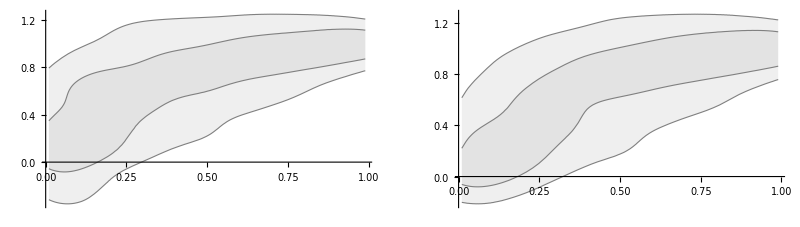

```mathematica
Clear[list1InterpSigmaCurves, plotSigmaRegions];
list1InterpSigmaCurves::usage = "list1InterpSigmaCurves[blueplot] provides a list of 4 interpolated curves in the following order:"<> 
    "{1σLowerLimit, 1σUpperLimit, 2σLowerLimit, 2σUpperLimit}. /n"<>
    "The plot to be provided (blueplot) can be generated by the function plotBlue.";
list1InterpSigmaCurves[plotblue_] := Block[
  {
    sigmaContoursList,
    curveSigma, 
    curveOrder, 
    curve2SigmaNeg, 
    curve1SigmaNeg, 
    curve1SigmaPlus, 
    curve2SigmaPlus
  },
  sigmaContoursList = Cases[
    Normal @ FullForm @ First @ plotblue,
    Line[pts_] :> pts,
    Infinity
  ];
  curveSigma[n_] := Interpolation[
    Sort@sigmaContoursList⟦n⟧,
    Method -> "Spline", 
    InterpolationOrder-> 2
  ];
  curveOrder = Ordering @ Table[curveSigma[n][0.5], {n, 1, 4}];
  curve2SigmaNeg = curveSigma[curveOrder⟦1⟧];
  curve1SigmaNeg = curveSigma[curveOrder⟦2⟧];
  curve1SigmaPlus = curveSigma[curveOrder⟦3⟧];
  curve2SigmaPlus = curveSigma[curveOrder⟦4⟧];
  {
    curve1SigmaNeg,
    curve1SigmaPlus,
    curve2SigmaNeg, 
    curve2SigmaPlus
  }
];

plotSigmaRegions::usage = 
  "plotSigmaRegions[curvesSigma, xLimit1, xLimit2] yields a plot with the 1 and 2 sigma regions from xLimit1 to xLmit2. \n" <>
  "The standard values of xLimit1 and xLimit2 are 0.2 and 0.9. \n" <>
  "The input to be provided, curvesSigma, can be generated by list1InterpSigmaCurves.";
  
plotSigmaRegions[curvesSigma_, xLimit1_:0.01, xLimit2_:0.99] := Plot[
  {
    curvesSigma[[3]][r],
    curvesSigma[[1]][r],
    curvesSigma[[2]][r],
    curvesSigma[[4]][r]
  },
  {r, xLimit1, xLimit2},
  Filling -> {{1 -> {3}, GrayLevel[0.7]}, {2 -> {4}}},
  PlotStyle -> {{Thickness[0.002], Gray}, {Thickness @ 0.002, Gray}},
  FillingStyle -> {GrayLevel[0.7], Opacity @ 0.05}
];

(*EXECUTION*)

{plotSigmaRegionsRAR, plotSigmaRegionsRARNoBulge} = plotSigmaRegions[list1InterpSigmaCurves[#]] & /@ {plotBlueRAR, plotBlueRARNoBulge};

GraphicsRow[
  {plotSigmaRegionsRAR, plotSigmaRegionsRARNoBulge},
  ImageSize -> 800
]
```

### I.2.1. Exporting the σ regions into a almost-paper-ready table (uncomment to export the files)

```mathematica
Clear[exportSigmaList]
exportSigmaList::usage = "curvesSigmaList[listOfCurves, rnMin, rnMax, step] generates 1σ and 2σ limiting curves in a close-to-paper-ready formated table, /n"<>
  "with rMin < r < rMax, in steps provided by step (optional, 0.02 being standard). The listOfCurves can be generated by list1InterpSigmaCurves./n"<>
  "exportSigmaList does not exports any file, but prepares the list to be exported.";

exportSigmaList[list1IpSigmaCurves_, rnMin_, rnMax_, step_:0.025] := Block[
  {header, tab, rn, nF, tabAux},
  header = {"# rn", "1σLower", "1σUpper", "2σLower", "2σUpper"};
  nF := NumberForm[#, {4, 3}] &;
  tabAux = Table[list1IpSigmaCurves[[n]]@rn, {n, 4}];
  tab = Table[
    nF /@ Flatten[{rn, tabAux}],
    {rn, rnMin, rnMax, step} 
  ];
  Join[{header}, tab]
];

list1InterpCurvesRAR = list1InterpSigmaCurves[plotBlueRAR];
list1InterpCurvesRARNoBulge = list1InterpSigmaCurves[plotBlueRARNoBulge];

 
Export["sigmaRegionsRAR.csv", exportSigmaList[list1InterpCurvesRAR, 0.025, 1]];
Export["sigmaRegionsRARNoBulge.csv", exportSigmaList[list1InterpCurvesRARNoBulge, 0.025, 1]];
```

## II. Burkert application

### II.1 Burkert definition and limiting cases

Using rcn for the normalized rc: rc/Rmax and rn for the normalized radius: r/Rmax, the mass and the additional normalized velocity can be them easily computed:

plotBurkertGrayRed:

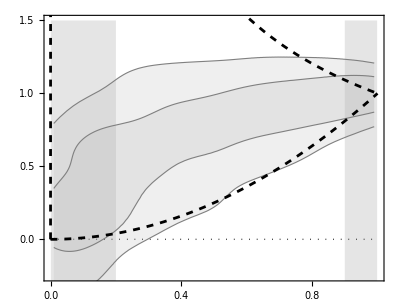

```mathematica
ρbrkt[rn_, rcn_, ρ0_] = ρ0/((1+rn/rcn)(1+rn^2/rcn^2));
Mbrkt[rn_, rcn_, ρ0_] = 4 π Rmax^3 Integrate[ρbrkt[rnprime,rcn,ρ0] rnprime^2,{rnprime,0,rn}, Assumptions-> {rn>0, rcn>0}];

VVbrkt[rn_, rcn_, ρ0_, Rmax_] = (G / Rmax) * Mbrkt[rn, rcn, ρ0] / rn;

δVbrkt[rn_, rcn_] = FullSimplify[
  VVbrkt[rn, rcn, ρ0, Rmax] / VVbrkt[1, rcn, ρ0, Rmax],
  Assumptions -> {0 < rn < 1, 0 < rcn < 1, 0 < Rmax}
];

plotBackground[upperLimit_] := nPlot[
  100,
  {rn, 0, 1},
  PlotRange -> {{0, 1}, {-0.25, upperLimit}},
  AspectRatio -> (1 / 1.3),
  GridLines -> None, 
  Prolog -> {
    Dotted,
    Line @ {{0, 0}, {1, 0}},
    Gray,
    Opacity[0.2], 
    Rectangle[{0.001, -0.5},{0.2, upperLimit}],
    Rectangle[{0.9, -0.5},{0.999, upperLimit}]
  }
];


plotBurkertGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVbrkt[rn, 1000], 
        δVbrkt[rn, 0.001]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotBurkertGrayRed:"];
Print@plotBurkertGrayRed;
```

### II.2. Burkert rcn Highest Density Regions

I want to find the values of rcn that best describe the n-sigma regions.

To this end, I have the find the minimum of the following integral (an extension of the χ^2 definition):

Performing the optimization.

rcn 1σ bounds:   {0.166051,0.606429}

rcn 2σ bounds:   {0.0989305,35.7141}

plotBurkertGlobalBestFit:

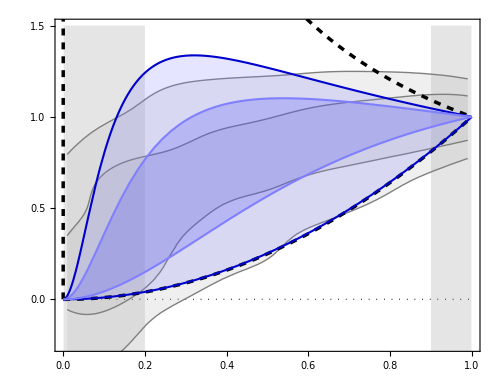

```mathematica
Clear[chi2Upper, chi2Lower];
chi2Upper[rcn_?NumberQ, nσ_]:= (*chi2Upper[rcn, nσ] =*) NIntegrate[
  (upperBound[nσ][rn] - δVbrkt[rn,rcn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rcn_?NumberQ, nσ_]:= chi2Lower[rcn, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVbrkt[rn,rcn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.01;
rnEnd=0.99;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

rcnUpper[2] = rcn /. NMinimize[{chi2Upper[rcn,2],rcn>0},{rcn,0,10}][[2]];
rcnUpper[1] = rcn /. NMinimize[{chi2Upper[rcn,1],rcn>0},{rcn,0,10}][[2]];
rcnLower[2] = rcn /. NMinimize[{chi2Lower[rcn,2],rcn>0},{rcn,0,10}][[2]];
rcnLower[1] = rcn /. NMinimize[{chi2Lower[rcn,1],rcn>0},{rcn,0,10}][[2]];

Echo[{rcnUpper[1], rcnLower[1]}, "rcn 1σ bounds: "];
Echo[{rcnUpper[2], rcnLower[2]}, "rcn 2σ bounds: "];

plotBurkertGlobalBestFit = Show[
  {
    plotBurkertGrayRed,
    Plot[
      {
        δVbrkt[rn, rcnUpper @ 2],
        δVbrkt[rn, rcnUpper @ 1],
        δVbrkt[rn, rcnLower @ 2],
        δVbrkt[rn, rcnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotBurkertGlobalBestFit:"];
Print@plotBurkertGlobalBestFit;

Export["plotBurkertGlobalBestFit.pdf", plotBurkertGlobalBestFit];
```

### II.3. Comparison with the rcn distribution found from the individual Burkert fits

The code below uses an older approach, but it works (compare with the Palatini approach)

1σ limits from individual fits:{0.107916, 0.49}

1σ limits from NAV method:{0.166051, 0.606429}

Lower and upper rcn limits used for the individual Burkert fits: {0, 100}

rcnDistributionHistogram for 1σ:

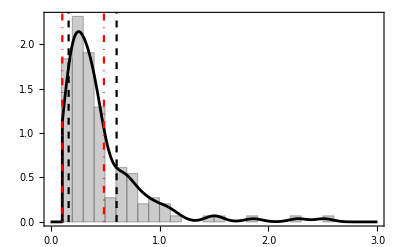

2σ limits from individual fits:{0.107916, 1.16}

2σ limits from NAV method:{0.0989305, 35.7141}

Lower and upper rcn limits used for the individual Burkert fits: {0, 100}

rcnDistributionHistogram for 2σ:

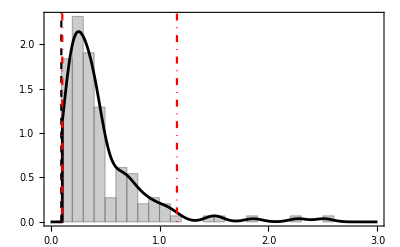

```mathematica
(*rcn values outside the upper and lower limits are not considered*)
(*The upper limit is important to eliminate those cases that are essentially infinity,
these also pose technical difficulties for the kernel density estimation.
The lower limit may be important since we have droppend all data with rn < 0.2,
There are galaxies that use the DM profile to do a quick rise of the rotation curve.*)

Clear[statusHistogram, nSigmas, rcnLowerLimit, rcnUpperLimit];

statusHistogram[nSigmas_, rcnLowerLimit_, rcnUpperLimit_]:= Block[{},
  Rmax[i_] := Last @ gd[Rad, i];
  rc[i_] := globalData⟦i, colrc⟧ ;
  posExcluded = Position[Table[galdataRAR @ n, {n, 1, 175}], {}];
  RmaxXrcAll = Table[{Rmax @ i, rc @ i}, {i, 1, 175}];
  RmaxXrc = Delete[RmaxXrcAll, posExcluded];
  rcnDataAll =  (Divide @@@ RmaxXrcAll)^-1;
  rcnData =  (Divide @@@ RmaxXrc)^-1;
  histoOptions =   Sequence @@ {
    Frame -> True, 
    Axes -> False, 
    ChartStyle -> Directive[EdgeForm[GrayLevel[0.4]], GrayLevel @ 0.8],
    FrameStyle -> Directive[GrayLevel[0.4], 16],
    PlotRangeClipping -> True,
    FrameTicks -> {{LinTicks, StripTickLabels@LinTicks2}, {LinTicks, StripTickLabels@LinTicks2}}
  };
  
  rcnDataWithoutOutliers = Select[rcnData, rcnLowerLimit < # < rcnUpperLimit &]; 
  dist = SmoothKernelDistribution[
    rcnDataWithoutOutliers, 
    silvermanBw[rcnDataWithoutOutliers], 
    MaxExtraBandwidths -> 0,
    InterpolationPoints -> 10^4
  ];

  pdfValuesForContours = Block[
    {
      positionAtCdf, oneSigmaProbability, twoSigmaProbability, positionsAtPdf, pdfList,
      pdfSortList, cdfSortList
    },
    oneSigmaProbability = NProbability[Less[-1, x, 1], Distributed[x, NormalDistribution[]]];
    twoSigmaProbability = NProbability[Less[-2, x, 2], Distributed[x, NormalDistribution[]]];
    pdfList = Table[
      PDF[dist,x],
      {x, 0, 3, 0.01}
    ];
    pdfSortList = Reverse @ Sort @ Flatten @ pdfList;
    cdfSortList = Accumulate[pdfSortList] / Total[pdfSortList] ;
    positionAtCdf[probability_] := FirstPosition[cdfSortList, p_ /; GreaterEqual[p, probability]];
    positionsAtPdf = Flatten @ Map[positionAtCdf, {oneSigmaProbability, twoSigmaProbability}];
    pdfSortList⟦positionsAtPdf⟧
  ];

  sigmaContoursPlot = ContourPlot[
    PDF[dist,x],
    {x, 0, 3},
    {y,0, 2},
    Contours -> pdfValuesForContours, 
    PlotRange -> {{0., 3}, All}
  ];

  sigmaContoursList = Cases[
    Normal @ FullForm @ First @ sigmaContoursPlot,
    Line[pts_] :> pts,
    Infinity
  ];

  maxPDF = x /. Last @ Maximize[PDF[dist, x], x];

  rcnRootsSigma[i_] := Quiet[
    FindRoot[
      PDF[dist,x]==pdfValuesForContours[[i]], #
    ] & /@ {{x,0,maxPDF}, {x,maxPDF,3}},
    FindRoot::brmp
  ];

  {rcnLow @ 1, rcnHigh @ 1} = x /. rcnRootsSigma[1];
  {rcnLow @ 2, rcnHigh @ 2} = x /. Quiet[rcnRootsSigma[2], FindRoot::brmp];

  lines = {
    Dashed, 
    Thickness @ 0.004, 
    Line @ {{rcnUpper @ nSigmas, 0}, {rcnUpper @ nSigmas, 100}},
    Line @ {{rcnLower @ nSigmas, 0}, {rcnLower @ nSigmas, 100}}
  };

  lines2= {
    Red,
    DotDashed, 
    Thickness @ 0.004, 
    Line @ {{rcnLow @ nSigmas, 0}, {rcnLow @ nSigmas, 100}},
    Line @ {{rcnHigh @ nSigmas, 0}, {rcnHigh @ nSigmas, 100}}
  };

  rcnDistributionHistogram := Histogram[
    rcnDataWithoutOutliers,
    {0.1}, 
    "PDF", 
    PlotRange -> {{0, 3}, All},
    Frame -> True, 
    Axes -> False, 
    Epilog -> {lines, lines2}, 
    histoOptions
  ];

  Echo[ToString@nSigmas <>"σ limits from individual fits:" <> ToString@{rcnLow@nSigmas, rcnHigh@nSigmas}];
  Echo[ToString@nSigmas <>"σ limits from NAV method:" <> ToString@{rcnUpper@nSigmas, rcnLower@nSigmas}];
  Echo["Lower and upper rcn limits used for the individual Burkert fits: " <> ToString[{rcnLowerLimit, rcnUpperLimit}]];
  Echo["rcnDistributionHistogram for "<> ToString@nSigmas <>"σ:"];
  Print@Show[{rcnDistributionHistogram, nPlot[PDF[dist,x], {x,0,3}, PlotRange -> All]}]
];

statusHistogram[1, 0, 100];

statusHistogram[2,0,100];
```

## III. Exponential profiles for stars and gas: Necessary for modified gravity applications

## III.1. Stellar contribution

```mathematica
Clear[vExp, fitExpVdisk, fitExpVdiskPlot, chi2, associationFitExpVdisk];

(*vExp comes from Binney & Tremaine 2nd Ed., eq.(2.165)*)
vExp[R_,logSigma0_,h_]= Block[{y}, 
  y = R/(2 h);
  kpc Sqrt[4 π G0 10^logSigma0 h y^2 (BesselI[0,y] BesselK[0,y] - BesselI[1,y] BesselK[1,y])]
];

chi2[model_List, dataObs_List, uncertainty_List] := chi2[model, dataObs, uncertainty]  = Total[(model-dataObs)^2/uncertainty^2];

associationFitExpVdisk::usage="associationFitExpVdisk[data(R x Vdisk)] fits the radial vs disk velocity curve data as a rotation curve for an exponential disk and returns an association with several data. "<>
  "For fitting, it is assumed an uncertainty of 10% on the velocity. The important point is not the porportionality constant, but that the uncertainty is proportional to the velocity. "<>
  "If data = {},  associationFitExpVdisk returns {}.";

associationFitExpVdisk[dataRVdisk_List] := fitExpVdisk[dataRVdisk] = Block[
  {sol, R, h, bestLogSigma0, besth, logSigma0, listModel, uncertainty, rMax, solExtended},
  If[
    dataRVdisk=={}, 
    Return[{}]
  ];
  rMax = Last @ dataRVdisk[[All, 1]];
  listModel = vExp[# , logSigma0, h] & /@ dataRVdisk[[All,1]];
  uncertainty = Max[{0.10 dataRVdisk[[#, 2]], 2}] & /@ Range@Length@dataRVdisk; (*Assumes uncertainty of 10% or 2 km/s. *)
  sol = NMinimize[
    {chi2[listModel, dataRVdisk[[All, 2]], uncertainty], h > 0, logSigma0 > 1},
    {{logSigma0, 6, 10}, {h, 0.5, 10}},
    Method-> Automatic
  ];
  (*{logSigma0, h, Chi2, Number of data points }*)
  solExtended = {First@sol, First@sol/(Length[dataRVdisk] - 2), logSigma0, h, h/rMax, rMax, Length[dataRVdisk]} /. Last@sol;
  AssociationThread[{"Chi2", "Chi2red", "logSigma0", "h", "hn", "rMax", "dataPoints"}, solExtended]
];

plotFittedExpVdisk[dataRVdisk_List, bestVdiskValues_List]:= Block[
  {vMax, bestLogSigma0, besth, rMax},
  If[
    dataRVdisk=={}, 
    Return[{}]
  ];
  {bestLogSigma0, besth} = bestVdiskValues;
  vMax = Max @ dataRVdisk[[All, 2]];
  rMax = Last @ dataRVdisk[[All, 1]];
  Show[
    {
      ListPlot[
        dataRVdisk,
        PlotRange -> {{0, 1.1 * rMax}, {0, 1.1 * vMax}}
      ],
      Plot[vExp[R, bestLogSigma0, besth], {R, 0, 100}, PlotRange -> All]
    }
  ]
];
```

```mathematica
Echo["Computing datasetExpVdiskNoBulge. This takes some seconds."];
datasetExpVdiskNoBulge = Dataset[
  DeleteCases[ 
    associationFitExpVdisk[gdRBulgeless[{Rad, Vdisk}, #]] & /@ Range[175], 
  {}]
] // EchoTiming
```

Computing datasetExpVdiskNoBulge. This takes some seconds.

41.6568

```mathematica
Export["headerAux.txt", {
  "# Additional velocity distribution: a fast sample analysis for dark matter or modified gravity models",
  "# by A. Hernandez-Arboleda, D. C. Rodrigues, A. Wojnar",
  "# ",
  "# The complete Table B1 data: the best fit results of an exponential model for the stellar component of 122 SPARC galaxies.",
  "# First column: best-fit disk scale length (h).",
  "# Second column: best-fit central surface brightness (logSigma0).",
  "# Third column: normalized disk scale length (hn).",
  "# Fourth column: the minimum chi-squared value (Chi2).",
  "# Fifth column: the number of galaxy data points that were used for the fit (dataPoints).", 
  "# ",
  "# "
}];

datasetStarsExport = datasetExpVdiskNoBulge[All,{"h","logSigma0", "hn","Chi2", "dataPoints"}];
Export["StellarExponentialBestFitAux.tsv", datasetStarsExport, Alignment-> Left, "TextDelimiters"->None];

Run["cat headerAux.txt StellarExponentialBestFitAux.tsv > StellarExponentialBestFit.tsv"]; (*It is only guaranteed to work in Unix systems. Sorry Windows...*)

DeleteFile["headerAux.txt"];
DeleteFile["StellarExponentialBestFitAux.tsv"];
```

### III.1.1. The hn distribution

1σ limits:  {0.0629196,0.293442}

2σ limits:  {0.0299119,0.474179}

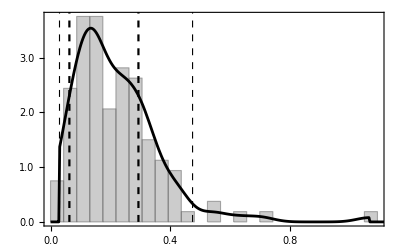

```mathematica
listhn= Normal @ datasetExpVdiskNoBulge[All, "hn"];

dist = SmoothKernelDistribution[
  listhn,
  silvermanBw @ listhn,
  MaxExtraBandwidths -> 0,
  InterpolationPoints -> 10^4 (*This is a large number, it has no relevant impact on speed *)
];

listHDPDFlimits = FindHDPDFValues[dist, oneAndTwoSigma];

list2PointsXPDF = {dist["InterpolationPoints"], dist["PDFValues"]}ᵀ;
positionMaxPDF = First @ Last @ SortBy[list2PointsXPDF, Last];

rootsSigma[i_] := (FindRoot[
  PDF[dist, x] == listHDPDFlimits[[i]], 
  #, 
  MaxIterations -> 1000
] & /@ {{x, 0, positionMaxPDF}, {x, positionMaxPDF, 1}}) ~ Quiet ~ FindRoot::brmp;

{hnLow[1], hnHigh @ 1} = x /. rootsSigma[1];
{hnLow[2], hnHigh @ 2} = x /. rootsSigma[2];

Clear @ lines;
lines[nSigmas_] := {
  Dashed,
  Thickness[0.004 / nSigmas],
  Line @ {{hnLow @ nSigmas, 0}, {hnLow @ nSigmas, 100}},
  Line @ {{hnHigh @ nSigmas, 0}, {hnHigh @ nSigmas, 100}}
};

Echo[{hnLow @ 1, hnHigh @ 1} ,"1σ limits:"];
Echo[{hnLow @ 2, hnHigh @ 2} ,"2σ limits:"];

Show[
  {
    Histogram[listhn,
      {silvermanBw @ listhn},
      "PDF", histoOptions, Epilog -> {lines @ 1, lines @ 2},
      PlotRange -> All
    ],
    nPlot[PDF[dist, x], {x, 0, 10}]
  }
]
```

### III.1.2. Deriving the hGasn, frho and fh values for each galaxy

hGas is the h value for the gas distribution.
hGasn is the hn value for the gas distribution.
frho is the ratio between the gas to stellar central density.
fh is the ratio between hn and hGasn.

#### logSigma0gas e hGasn

```mathematica
Clear[associationFitExpVgas];
associationFitExpVgas[dataRVgas_List] := associationFitExpVgas[dataRVgas] = Block[
  {sol, R, h, bestLogSigma0, besth, logSigma0, listModel, uncertainty, rMax, solExtended},
  If[
    dataRVgas=={}, 
    Return[{}]
  ];
  rMax = Last @ dataRVgas[[All, 1]];
  listModel = vExp[# , logSigma0, h] & /@ dataRVgas[[All,1]];
  uncertainty = Max[{0.10 dataRVgas[[#, 2]], 2}] & /@ Range@Length@dataRVgas; (*Max[10%, 2 km/s] uncertainty, inspired on distance error together with a minimum one.*)
  sol = NMinimize[
    {chi2[listModel, dataRVgas[[All, 2]], uncertainty], 100 rMax > h > 0.1, logSigma0 > 0.5},
    {{logSigma0, 3, 10}, {h, 3, 30}},
    Method-> Automatic
  ];
  (*{logSigma0, h, Chi2, Number of data points }*)
  solExtended = {First@sol, First@sol/(Length[dataRVgas] - 2), logSigma0, h, h/rMax, rMax, Length[dataRVgas]} /. Last@sol;
  AssociationThread[{"Chi2", "Chi2red", "logSigma0Gas", "hGas", "hGasn", "rMax", "dataPoints"}, solExtended]
];
```

```mathematica
Echo["Computing datasetExpVgasNoBulge. This takes some seconds."];
datasetExpVgasNoBulge = Dataset[
  DeleteCases[ 
    associationFitExpVgas[gdRBulgeless[{Rad, Vgas}, #]] & /@ Range[175], 
  {}]
] // EchoTiming
```

Computing datasetExpVgasNoBulge. This takes some seconds.

53.2908

```mathematica
Export["headerGasAux.txt", {
  "# Additional velocity distribution: a fast sample analysis for dark matter or modified gravity models",
  "# by A. Hernandez-Arboleda, D. C. Rodrigues, A. Wojnar",
  "# ",
  "# This file: Best fit results of an exponential model for the gaseous component of 122 SPARC galaxies.",
  "# First column: best-fit disk scale length (hGas).",
  "# Second column: best-fit central surface brightness (logSigma0Gas).",
  "# Third column: normalized disk scale length (hGasn).",
  "# Fourth column: the minimum chi-squared value (Chi2).",
  "# Fifth column: the number of galaxy data points that were used for the fit (dataPoints).", 
  "# ",
  "# "
}];

datasetGasExport = datasetExpVgasNoBulge[All,{"hGas","logSigma0Gas", "hGasn","Chi2", "dataPoints"}];
Export["GasExponentialBestFitAux.tsv", datasetGasExport, Alignment-> Left, "TextDelimiters"->None];

Run["cat headerGasAux.txt GasExponentialBestFitAux.tsv > GasExponentialBestFit.tsv"]; (*It is only guaranteed to work in Unix systems. Sorry Windows...*)

DeleteFile["headerGasAux.txt"];
DeleteFile["GasExponentialBestFitAux.tsv"];
```

#### frho, fh and hn vectors

```mathematica
list1hn = Normal@datasetExpVdiskNoBulge[All, "hn"];
list1hGasn = Normal@datasetExpVgasNoBulge[All, "hGasn"];
list1logSigma0 = Normal@datasetExpVdiskNoBulge[All, "logSigma0"];
list1logSigmaGas0 = Normal@datasetExpVgasNoBulge[All, "logSigma0Gas"];

list1frho = list1logSigmaGas0/ (0.5 list1logSigma0) (*The 0.5 comes from the mass to light ratio*);
list1fh = list1hn/ list1hGasn;
```

## IV. Palatini

## IV.1. Additional contribution from stars only (to warm up)

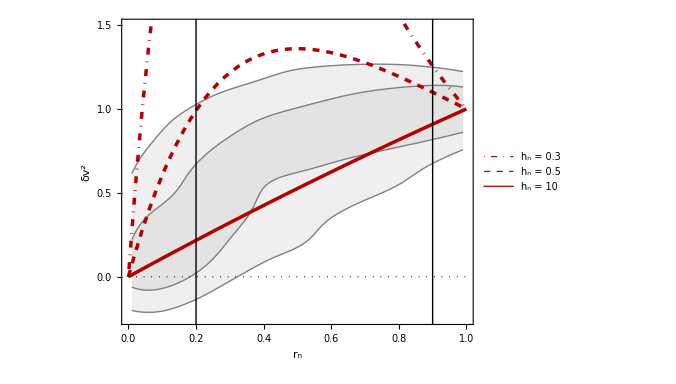

```mathematica
δvP2[rn_, hn_] = rn Exp[(1-rn) / hn];

plot100 := nPlot[
  100,
  {rn, 0, 1},
  PlotRange -> {{0, 1}, {-0.25, 1.5}},
  AspectRatio -> (1 / 1.3),
  GridLines -> None, 
  ImageSize -> 500, 
  FrameStyle -> 18, 
  Epilog -> 
  {
    Line[{{0.2, -0.5}, {0.2, 2}}],
    Line @ {{0.9, -0.5}, {0.9, 2}},
    Dotted,
    Line @ {{0, 0}, {1, 0}}
  }
];

plotPalatiniStars := Plot[
  {δvP2[rn, 0.3], δvP2[rn, 0.5], δvP2[rn, 10]},
  {rn, 0, 1},
  PlotRange -> All,
  PlotStyle -> 
  {
    {Thickness[0.005], DotDashed, Darker[Red, 0.3]},
    {Thickness[0.005], Dashed, Darker[Red, 0.3]},
    {Thickness[0.005], Darker[Red, 0.3]}
  },
  PlotLegends->Placed[
    {
      Style["h_n = 0.3",17, FontFamily->Times], 
      Style["h_n = 0.5",17, FontFamily->Times], 
      Style["h_n = 10",17, FontFamily->Times]
    },
    {{0.76,0.26},{0.5,0.5}}
  ]
];

Show[{plot100, plotSigmaRegionsRARNoBulge, plotPalatiniStars}, 
  FrameLabel->{Style["r_n", 20, FontFamily->Times], Style["δv^2", 20, FontFamily->Times]}
]
```

Conclusions: there is a significant  region that cannot covered by this Palatini case. 
The curve for hn=10 is essentially the same for any curve with hn > 10: a straightline.
Also, the necessary hn values to cover  the most dense regions are unrealistic, as detailed below.

## IV.2. Stars and Gas for Palatini

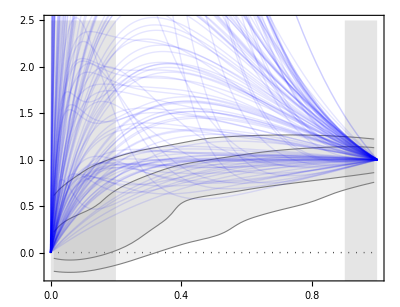

```mathematica
δvP2g[rn_, hn_, fh_, frho_]= (rn ( ⅇ^(-rn/hn)+  frho  fh ⅇ^(- fh rn/hn)))/( ⅇ^(-1/hn)+  frho fh  ⅇ^(- fh /hn));
δvPalatini[rn_, gal_] := δvP2g[rn, list1hn[[gal]], list1fh[[gal]], list1frho[[gal]]];
Show[plotBackground[2.5],
  plotSigmaRegionsRARNoBulge,
  Plot[Evaluate[δvPalatini[rn, #] & /@ Range@122], {rn, 0, 1}, 
PlotRange -> All, 
PlotStyle-> Directive[Opacity[0.1],Blue, Thick]]
]
```

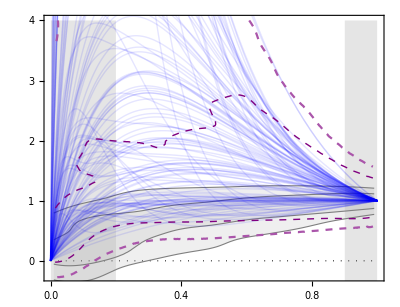

```mathematica
Clear @ list2δVVmodel;
list2δVVmodel[gal_] := Table[{rn, δvPalatini[rn, gal]}, {rn, RandomReal[1,200]}];
list2δVVmodelAll = Flatten[DeleteCases[list2δVVmodel /@ Range @ 122, {}], 1];

distPalatini = distributionSilverman @ list2δVVmodelAll;
list1LimitsSigmaPalatini = FindHDPDFValues[distPalatini, oneAndTwoSigma];
(*plotBluePalatini = plotBlue[list2δVVmodelAll, list1LimitsSigmaPalatini, {{xmin, xmax - 0.01}, {-0.5, 2.5}}, PlotRange -> {{0, 0.99}, {-0.5, 2.5}}] *)

plotPalatiniCurves = Plot[Evaluate[δvPalatini[rn, #] & /@ Range@122], {rn, 0, 1}, PlotRange -> All, PlotStyle-> Directive[Opacity[0.1],Blue, Thick]];

plotPalatiniContours = ContourPlot[
{
PDF[distPalatini, {x,y}] == list1LimitsSigmaPalatini[[1]], PDF[distPalatini, {x,y}] == list1LimitsSigmaPalatini[[2]]
}, 
{x,0,1}, {y,-0.5, 4.0},  
ContourStyle-> {Directive[Purple, Dashed, Thick], Directive[Lighter@Purple, Dashed]}];

Show[
plotBackground[4.0],
plotSigmaRegionsRAR,
plotPalatiniCurves,
plotPalatiniContours
]

Export["plotdeltaVPalatini.pdf", %];
```

## V. MOND

## V.1 MOND observational data without approximations (all 153 galaxies)

```mathematica
Clear[a0, aNewtList, aNewt, ΔVVmodel, rmax, interpolVbar, interpolVbarSquared, VVmodel, δVVmodel];

rmax[gal_] := Last[gdR[Rad, gal]];

aNewtList[gal_]:=Block[{vvbar, aux},
  vvbar = squareSign[gdR[Vbar, gal]];
  (*vvbar = Total[{ squareSign[#1], 0.5 squareSign[#2], 0.6 squareSign[#3] }] & @@@ gdR[{Vgas, Vdisk, Vbulge},gal];*)
  aux = {gdR[Rad,gal], vvbar/(kpc gdR[Rad,gal])}ᵀ;
  Prepend[aux, {0,0}]
];

aNewt[R_, gal_] := aNewt[R, gal] = Interpolation[aNewtList[gal], Method->"Spline", InterpolationOrder->2][R];

VVmodel[R_, gal_] := R kpc aNewt[R, gal]/(1 - ⅇ^(-√(RealAbs[aNewt[R, gal]]/a0)));

ΔVVmodel[R_, gal_] := VVmodel[R, gal] - aNewt[R, gal] R kpc ;

δVVmodel[rn_, gal_] := If[gdR[Rad, gal]=={}, 
  {}, 
  ΔVVmodel[rn rmax[gal], gal] / ΔVVmodel[rmax[gal], gal]
];
```

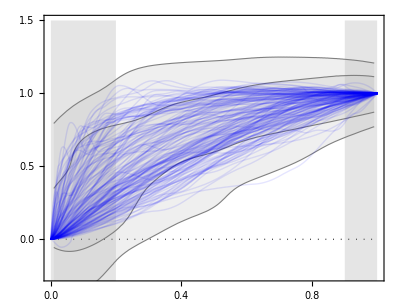

```mathematica
a0=   1;
Show[plotBackground[1.5],
plotSigmaRegionsRAR,
Plot[Evaluate[δVVmodel[rn, #]& /@ Range@175], {rn,0,1}, PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All]]
Export["plotdeltaVmonda01.pdf", %];
```

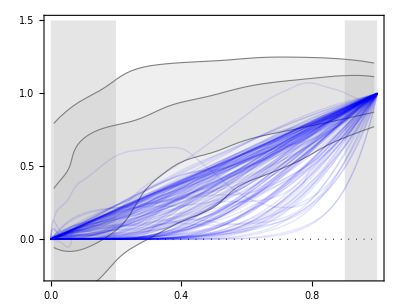

```mathematica
a0=  10^-15;
Show[plotBackground[1.5],
plotSigmaRegionsRAR,
Plot[Evaluate[δVVmodel[rn, #]& /@ Range@175], {rn,0,1},  PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All]]
Export["plotdeltaVmonda015.pdf", %];
```

The galaxy with a bump above 1 has the number 114. It has an unnusual feature: at about rn = 0.8 it has a local minimum in its acceleration. Hence, this oscilation above is not a numerical error, it reflects a property of this galaxy.

#### Comparison of the MOND distribution with the SPARC δv^2 distribution

```mathematica
a0 = 1.2 10^-13;
Clear @ list2δVVmodel;
list2δVVmodel[gal_] := If[gdR[Rad, gal] == {},
 {},
Table[{rn, δVVmodel[rn, gal]}, {rn, RandomReal[1,70]}]
];
list2δVVmodelAll = Flatten[DeleteCases[list2δVVmodel /@ Range @ 175, {}], 1];
```

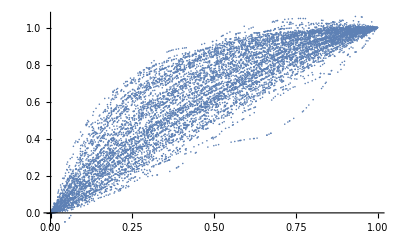

```mathematica
ListPlot @ list2δVVmodelAll
```

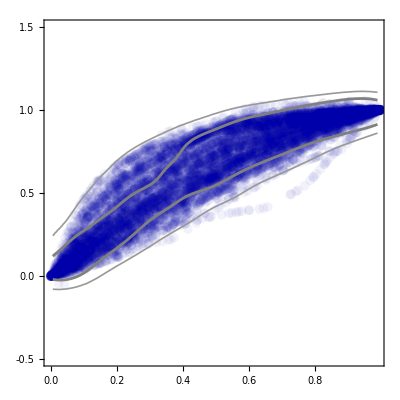

```mathematica
list1LimitsSigmaMondRaw = FindHDPDFValues[distributionSilverman @ list2δVVmodelAll, oneAndTwoSigma];
plotBlueMondRaw = plotBlue[list2δVVmodelAll, list1LimitsSigmaMondRaw, {{xmin, xmax - 0.01}, {-0.5, 1.5}}, PlotRange -> {{0, 0.99}, {-0.5, 1.5}}]
```

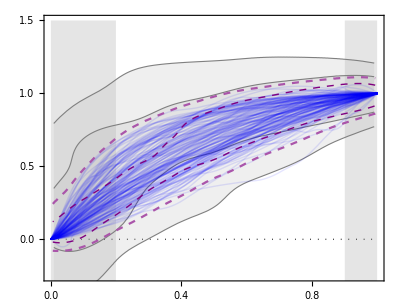

```mathematica
distMondRaw =distributionSilverman@list2δVVmodelAll;

plotMondCurves = Plot[Evaluate[δVVmodel[rn, #] & /@ Range@175], {rn, 0, 1}, PlotRange -> All, PlotStyle-> Directive[Opacity[0.1],Blue, Thick]];

plotMondContours = ContourPlot[
{
PDF[distMondRaw, {x,y}] == list1LimitsSigmaMondRaw[[1]], PDF[distMondRaw, {x,y}] == list1LimitsSigmaMondRaw[[2]]
}, 
{x,0,1}, {y,-0.5, 1.5},  
ContourStyle-> {Directive[Purple, Dashed, Thick], Directive[Lighter@Purple, Dashed]}];

Show[
plotBackground[1.5],
plotSigmaRegionsRAR,
plotMondCurves,
plotMondContours
]

Export["plotdeltaVmondPrincipal.pdf", %];
```

## V.2 MOND with exponential approximations : 122 galaxies

```mathematica
Clear[a0, rn, datasetDisk, datasetGas, auxTab, list1δVVMondExp, list2δVVMondExpAux, VVbarExp, aNewtExp, VVMondExp, δVVMondExp, numberGalaxies, nG, ΔVVMondExp, rMax, dataGal];

datasetDisk = datasetExpVdiskNoBulge;
datasetGas = datasetExpVgasNoBulge;

numberGalaxies = Length @ datasetDisk;
nG = numberGalaxies; (*122 galaxies without Bulge*)

VVbarExp[R_, logSigma0_, h_, logSigmaGas0_, hgas_] := 0.5 vExp[R, logSigma0, h]^2 + vExp[R, logSigmaGas0, hgas]^2;

dataGal[gal_] := dataGal[gal] = {
  datasetDisk[gal, "logSigma0"], 
  datasetDisk[gal, "h"], 
  datasetGas[gal, "logSigma0Gas"], 
  datasetGas[gal, "hGas"]
};

rMax[gal_] := rMax[gal] = datasetDisk[gal, "rMax"];

VVbarExp[R_, gal_Integer] := VVbarExp[R, Sequence @@ dataGal[gal]];

aNewtExp[R_, gal_] :=  VVbarExp[R, gal]/ (R kpc);

VVMondExp[R_, gal_] :=  R kpc aNewtExp[R, gal]/(1 - ⅇ^(-√(aNewtExp[R, gal] / a0)));

ΔVVMondExp[R_, gal_] := VVMondExp[R, gal] - VVbarExp[R, gal];

δVVMondExpAux[rn_, gal_Integer] := ΔVVMondExp[rn rMax[gal], gal] / ΔVVMondExp[rMax[gal], gal];

(*To speed up the plots, it is relevant to define δVVMondExp from a list of interpolated functions (list1δVVMondExp)*)
list1δVVMondExp[rni_] = Block[
  {list2δVVMondExpAux},
  list2δVVMondExpAux[gali_] := Prepend[
    Table[{rni,δVVMondExpAux[rni, gali]}, {rni, 0.05, 1, 0.05}], 
    {0,0}
  ];
  Table[
    Interpolation[list2δVVMondExpAux[gali]][rni], 
  {gali, nG}
  ]
];

δVVMondExp[rn_, gal_] :=  list1δVVMondExp[rn][[gal]]
```

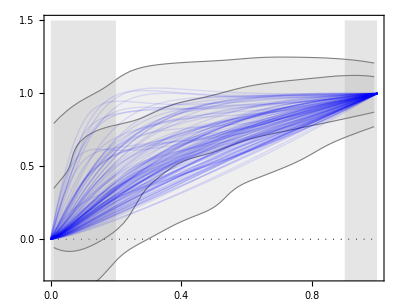

```mathematica
a0=   1;
Show[plotBackground[1.5],
plotSigmaRegionsRAR,
Plot[Evaluate[δVVMondExp[rn, #]& /@ Range @ nG], {rn,0,1}, PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All]]
Export["plotdeltaVmondExpa01.pdf", %];
```

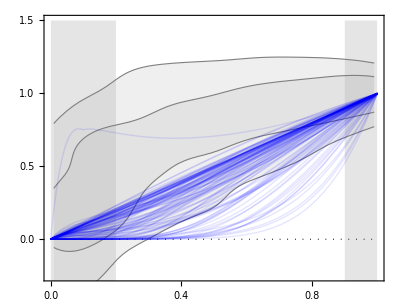

```mathematica
a0=   10^-15;
Show[plotBackground[1.5],
plotSigmaRegionsRAR,
Plot[Evaluate[δVVMondExp[rn, #]& /@ Range @ nG], {rn,0,1}, PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All]]
Export["plotdeltaVmondExpa015.pdf", %];
```

#### Comparison of the MONDExp distribution with the SPARC δv^2 distribution -- It takes minutes to run.

```mathematica
a0 = 1.2 10^-13;
Clear @ list2δVVmodel;
list2δVVmodel[gal_] := Table[{rn, δVVMondExp[rn, gal]}, {rn, RandomReal[1,70]}];
list2δVVmodelAll = Flatten[DeleteCases[list2δVVmodel /@ Range @ nG, {}], 1];
distMondExp =distributionSilverman@list2δVVmodelAll;

list1LimitsSigmaMondExp = FindHDPDFValues[distMondExp, oneAndTwoSigma];
```

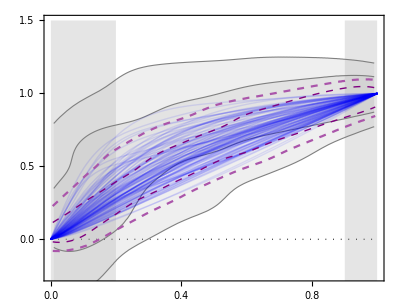

```mathematica
plotMondCurves = Plot[Evaluate[δVVMondExp[rn, #] & /@ Range@ nG], {rn, 0, 1}, PlotRange -> All, PlotStyle-> Directive[Opacity[0.1],Blue, Thick]];

plotMondContours = ContourPlot[
{
PDF[distMondExp, {x,y}] == list1LimitsSigmaMondExp[[1]], PDF[distMondExp, {x,y}] == list1LimitsSigmaMondExp[[2]]
}, 
{x,0,1}, {y,-0.5, 1.5},  
ContourStyle-> {Directive[Purple, Dashed, Thick], Directive[Lighter@Purple, Dashed]}];

Show[
plotBackground[1.5],
plotSigmaRegionsRAR,
plotMondCurves,
plotMondContours
]

Export["plotdeltaVmondExpPrincipal.pdf", %];
```

## VI. RGGR

```mathematica
(*phiDisk and phiGas come from Binney & Tremaine 2nd Ed., eq.(2.164a)*)
Clear[phiExpDisk, phiExpGal, phiExpGal, ΔVVRGGR, δVVRGGR]

phiExpDisk[R_,logSigma0_,h_] = Block[{y, logSigma0, h, R}, 
  y = R/(2 h);
  - 4 π G0 10^logSigma0 R (BesselI[0,y] BesselK[1,y] - BesselI[1,y] BesselK[0,y])
];

phiExpGal[R_, logSigma0_, h_, logSigmaGas0_, hGas_] = 0.5 phiExpDisk[R, logSigma0, h] + phiExpDisk[R, logSigmaGas0, hGas];

phiExpGal[R_, gal_Integer] := phiExpGal[R, gal] = phiExpGal[R, Sequence @@ dataGal[gal]];

ΔVVRGGR[R_, gal_] := - VVInfty VVbarExp[R, gal] / phiExpGal[R, gal];

δVVRGGRAux[rn_, gal_Integer] := δVVRGGRAux[rn, gal] =  ΔVVRGGR[rn rMax[gal], gal] / ΔVVRGGR[rMax[gal], gal];

(*To speed up the plots, it is relevant to define δVVMondExp from a list of interpolated functions (list1δVVMondExp)*)
l1δVVRGGR[rni_] = Block[
  {l2δVVRGGRAux},
  l2δVVRGGRAux[gali_] := Prepend[
    Table[{rni, δVVRGGRAux[rni, gali]}, {rni, 0.05, 1, 0.05}], 
    {0,0}
  ];
  Table[
    Interpolation[l2δVVRGGRAux[gali]][rni], 
  {gali, nG}
  ]
];

δVVRGGR[rn_, gal_] :=  l1δVVRGGR[rn][[gal]]
```

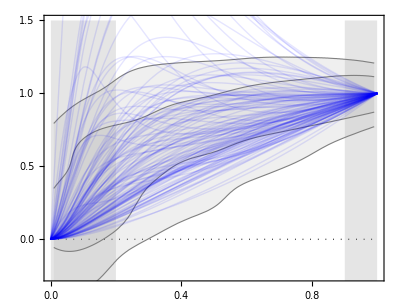

```mathematica
Show[
plotBackground[1.5],
plotSigmaRegionsRAR,
Plot[Evaluate[δVVRGGR[rn, #]& /@ Range @ nG], {rn,0,1}, PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All]]
```

```mathematica
l2δVVRGGRdiscrete[gal_] := Table[{rn, δVVRGGR[rn, gal]}, {rn, RandomReal[1,200]}];
l2δVVRGGRdiscreteAll = Flatten[l2δVVRGGRdiscrete /@ Range @ nG, 1];
distRGGR =distributionSilverman @ l2δVVRGGRdiscreteAll;

l1LimitsSigmaRGGR = FindHDPDFValues[distRGGR, oneAndTwoSigma];
```

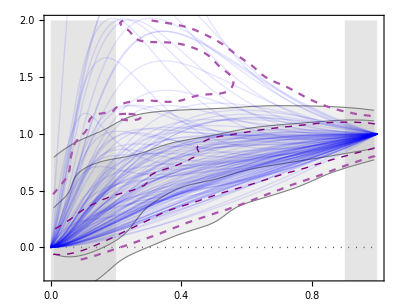

```mathematica
plotRGGRCurves = Plot[Evaluate[δVVRGGR[rn, #] & /@ Range@ nG], {rn, 0, 1}, PlotRange -> All, PlotStyle-> Directive[Opacity[0.1],Blue, Thick]];

plotRGGRContours = ContourPlot[
{
PDF[distRGGR, {x,y}] == l1LimitsSigmaRGGR[[1]], PDF[distRGGR, {x,y}] == l1LimitsSigmaRGGR[[2]]
}, 
{x,0,1}, {y,-0.5, 2.0},  
ContourStyle-> {Directive[Purple, Dashed, Thick], Directive[Lighter@Purple, Dashed]}];

Show[
plotBackground[2.0],
plotSigmaRegionsRAR,
plotRGGRCurves,
plotRGGRContours
]

Export["plotdeltaVRGGR.pdf", %];
```